```mathematica
parse[s_]:=ToExpression[StringReplace[s,"E"->"*10^"]]
```

```mathematica
plot[data_]:=Module[{primal,dual,gap,trainingerr},
primal=parse/@StringCases[data,RegularExpression["(?<=primal=)([E0-9\\.\\-]+)|(?<=primal = )([E0-9\\.\\-]+)"]];
dual=parse/@StringCases[data,RegularExpression["(?<=dual=)([E0-9\\.\\-]+)|(?<=dual = )([E0-9\\.\\-]+)"]];
gap=parse/@StringCases[data,RegularExpression["(?<=gap=)([E0-9\\.\\-]+)|(?<=gap = )([E0-9\\.\\-]+)"]];
trainingerr=parse/@StringCases[data,RegularExpression["(?<=Train error=\\()([E0-9\\.\\-]+)|(?<=Train error = \\()([E0-9\\.\\-]+)"]];
GraphicsGrid[{{
ListLinePlot[primal,PlotLabel->"Primal",PlotRange->All,GridLines->Automatic],
ListLinePlot[dual,PlotLabel->"Dual",GridLines->Automatic]},{
ListLinePlot[gap,PlotLabel->"Duality Gap",PlotRange->All,GridLines->Automatic],
ListLinePlot[trainingerr,PlotLabel->"Training err",GridLines->Automatic]
}},ImageSize->Large]
]
```

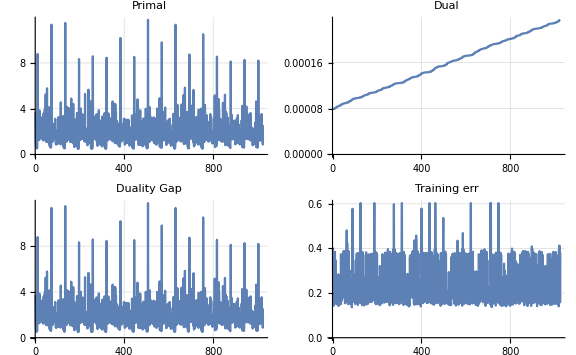

```mathematica
data=Import["/Users/thijs/Desktop/data/binary.txt"];
Show[plot[data],PlotLabel->Style["Results for four Binary features with StructSVMWithBCFW with interactions (chain copy)
",FontWeight->Bold,FontColor->Black]]
```

```mathematica
Export["out.png",%]
```

out.png

```mathematica
`
```

```mathematica
d=parse/@{"0.0","0.21615089584926772","14.45491359453363","0.3598886791157079","12.727249311179822","0.06180145611543882","0.624764621306645","4.634269109713577","0.07007245824320929","3.0658907750724116","0.06420416337371346","0.03946680800666824","0.8035908196666384","26.519777432794942","1.911807560519266","0.8539185834589346","0.018894906714546536","0.06149594627217824","2.668290553439965","11.452870421060183","0.037324878604746085","0.7143102850085022","0.20437500791984364","0.17302946345787773","1.170603648500654","0.10175461611905173","0.17716184154241824","0.15218079016705152","0.38641110847296256","0.04068215042802104","8.525629662888301","0.4994828795373113","0.450467312641015","0.9373786985536164","0.28819253311079923","0.06811264529456187","0.9728357574194558","2.2457999897158807","2.282295700948679","0.046494827922114915","0.07872193792455229","5.445856276546671","2.7924357780593185","0.39939455965894655","19.833896451654425","0.20760917108292176","0.00867944554024598","0.5349000268933471","2.75910863850358","0.046416924271390846","0.06464659583889108","2.2091305404990096","0.6151868245666702","2.656858885086395","1.3771363625386341","6.021583219594103","0.14793175103227624","0.12484189227090187","2.7771404705486216","0.09544461726883587","0.4856346684350127","0.5649119942520393","4.695641854719398","0.5881093895763199","14.167265623608927","1.4419207557536688","0.46595253663069625","0.24470575085198287","13.845591293671314","0.13572002968704894","0.07530671402580626","1.783956602575891","0.09145575964048885","0.007164752379472825","2.7616049484025362","0.3029283538532496","2.0621499340146268","0.27605220726542334","2.088105736318895","0.19440849372267627","0.4281766488961486","0.7975021686721198","0.012786225201914525","3.6684318426983493","0.1527348290953381","0.15681795426128223","1.1622445878223755","0.4379030871526321","0.8471196199846239","3.697635740623271","2.6209254248646388","0.2920021009078005","5.2826479304649965","1.5207366517250493","0.038486114470512506","0.09222564264483565","0.04995220342695475","6.45353696426093","0.8358293293421566","0.03253369927888014","2.3899138113655987","1.7400978830030887","9.75321746996897E-4","5.3135578597105","1.4973785340298318","0.13659682884643873","11.606685175367996","0.16182192611641827","0.11490197575784933","0.17722595266917418","6.497011103750814","0.887360572334801","0.47601995570388933","0.40311164954645845","0.2882776193371315","134.48729223347007","1.0622826085019088","13.841455917472887","0.5391569657966273","0.06232139774524978","3.650701881587785","0.06007255714975321","0.016585211266308658","0.39035252248265984","6.9834362235238725","0.004150693619862884","42.68610437598617","7.346457993242627","1.3651870885210096","0.34847224015800027","13.641439822729762","1.0988024025815475","0.5826521109204974","0.028421401539997733","0.6159572866741948","4.622642826348886","0.09823740983584105","0.457758540231514","8.987141731145467","0.1548546141232625","0.8967695228506672","0.10569707362561602","0.9185822042342314","0.4775382486492725","0.0015631688390743638","5.800314419253143","10.2469359443458","1.111082780277089","6.670400282807852","8.398615031287829","2.7112462498142555","3.2001001640696938","1.0291137420970013","0.4525380646905275","9.926428239104698","0.7265806316575841","0.4580799820296077","0.30278114260590766","0.09443088719541501","0.6726683408394551","2.709404111750238","2.7254014314259143","4.09673713933914","0.05115957376168765","0.110053239272291","5.007096796939905","1.8117312166762454","0.3527457011515268","16.665892468768003","1.016863585831451","0.2108634309490308","0.4297626719313961","8.285560159644067","0.7469253960167251","0.11076426392743427","0.4246305458157546","0.8066781340411074","5.297389138739581","0.6062121828999287","0.22565857631598762","0.009048315740252715","110.24928262360207","3.76350050915884","0.19949379689183586","0.009324148723520512","0.444786513078813","3.6196804101912976","0.2572386480016161","2.5280570610134196","30.203758188652852","1.9286985843797848","0.17357449266345365","25.556897487330865","1.201103803405882","0.489525974337372","0.07288911238281261","0.5971720805622693","4.271261371634935","0.14497159216829014","0.5419374359852138","2.6028220703612464","1.5337243857337814","0.615509603026057","0.07154325658012345","0.8831803854120246","0.34814363168182494","0.045839086387526914","4.952443427978748","8.995163739875677","1.1324985547791986","5.7587430843253555","7.463774260996232","4.873907607669642","0.11368603468052912","0.6027040345080416","0.38187976672421386","36.194713546370025","5.3154601939685096","2.288345789834517","0.7560553921894702","0.0695577418306384","2.638783203865302","1.0410000588674135","23.720175378406182","1.3258166737074397","0.1279738899542148","0.03367560021263972","5.186920678053831","1.4146301593070272","0.09132702564513548","10.49502375786041","0.18081901933952435","0.08563281283854433","0.12542888621516166","2.3053886094110085","3.154999583215843","2.939876716705517","2.768487441114993","0.7428842606311878","2.998538153356132","5.268253250157334","19.13331808684351","0.8321579420970681","0.059522990704419736","4.5274799437237","0.10928219769632011","0.3834499994142233","0.025988460804535034","0.20567837992142635","0.8302194773144816","8.746985110554434","3.4787261222456376","0.7262847867399832","0.3118016185868754","14.96037280820049","0.09293683089864964","0.08749436359865602","1.9903516418601002","0.05232680384712186","38.95434794204474","0.16254496691198528","0.4254766795760553","10.441340012786075","0.17292168853704448","0.5828221540517705","0.048286589439283684","0.7573471723497751","0.31909488633669425","0.013654657350124487","5.384398412845638","9.491073632704403","1.071930118203345","6.199363215771748","8.211539819650357","3.6239142625202607","4.601780132124725","0.6975589252038177","0.41664929185089183","9.512568167120182","0.55492529464705","0.568692901791995","0.45139187191738306","0.07593799063673015","0.5969971902775497","0.5041557165652163","14.811749706077642","6.181128901228265","0.022298763475899833","0.06232850257437382","4.970284830299322","1.290387112820913","0.23059061608642817","13.242180939818073","0.6749362310091713","0.15743159442873927","0.2717487886158108","4.69893606068152","2.10582362871004","1.3584986920371354","1.5757082490149934","1.1909530203043444","2.9894845040286557","3.171617402862597","12.316537014815117","0.6143020187385717","0.07103695434110834","5.9320057056801785","0.2547799118909257","0.36100391263334686","0.19195011371603132","1.2183369351984106","1.3684192711682666","12.76705623451203","5.003733067482495","1.5643975771876713","0.15807552852409248","25.47016202630259","0.6371080908499238","0.3414411161748868","0.004408618239243489","16.617869334723444","2.2752705116086847","0.1427518817970453","0.3379075729401346","2.6174284119283024","0.6918676601025385","0.30408622466438334","36.6875280158408","0.0643161434892614","9.844557603732683","0.1319854458446371","0.07609610156376877","0.006515551520687647","0.03259087742983099","1.391450063274422","0.32302320172868143","1.4079644589554559","0.037395789701447454","0.6510296342287304","0.6299613286891377","3.3267770536244727","0.8885668570355681","0.006841130211988894","0.23840302368541166","0.08212383963483243","0.32523724870498527","1.2619292470669552","0.81137870014541","1.975963023117309","0.013772452405792425","0.08962820160004698","5.0144009540535315","1.6669208983869084","0.1396312756408079","11.11629306429156","0.5892241523225117","0.0667421350822763","0.286399053102678","6.034970895791744","0.3962470184398084","0.13393153838543698","28.862759864720587","0.8486930784814812","1.774211348012511","0.5831374891068608","0.08428294178035613","0.1350882432524954","1.1654191295399778","1.1096602170684848","0.003927400127477318","0.27257487484044735","0.0243833140955628","0.3210732143180252","0.6179362028343819","8.437085337315178","3.3109893372808954","0.7258613853016567","0.2861159095836923","14.502278757154176","0.1333918680405688","0.08505661953898835","2.592705447600989","0.06181747124481139","37.798114573530015","0.16918820316197092","0.31079188611212405","2.5310930384012","0.055375744103476274","1.1264139849441808","0.13402235337048057","0.030486892321040706","0.1322874574335145","0.05162116180746525","5.369656328378143","8.543515564274104","1.0560914133292927","5.829342127475048","8.0340844281857","8.686271825289783","0.2620492654347118","0.6394895246535914","0.46270174925168106","8.349866609462333","0.6146999086780909","0.10380391283794958","0.06312074902106915","0.018706198723754813","0.49466841596241107","0.6899859193579598","5.57936833257315","6.660962563339957","0.03837423886517066","0.13963754952360186","4.818236926587631","1.8152659604999724","0.2706577518694301","13.632956414622736","1.2047677035019106","0.11650874274492087","0.3865513829284996","0.2610097009393168","34.74752037243205","0.028068765586130126","0.17773565434479904","7.391303589113464","59.887522899607276","4.70213457554299","18.47466702082845","2.1166224533923206","1.749622678845547","0.3645019535143033","0.004179452620792834","0.10091445042930991","0.18450380243287598","1.1489392112272208","0.3954389762189179","5.826633304395156","2.7640577771370998","1.1354042859899494","0.11037883618217206","24.294996025376072","0.5170073837451588","0.18473973549177028","0.2926124672295062","0.08096309894325322","0.1438484289380233","0.15651648767824128","0.2653413661032459","7.056806877778066","0.14795591527234442","0.3849420971946489","0.018786002580609112","1.2404368594841377","0.1407398489546744","0.02878383272361098","4.780459643529423","8.51309552551747","1.025461083276858","5.4670295200506995","7.427742524361362","7.9680978448296385","0.15477462562584832","0.6436861660945801","0.47743051741496","8.079378214062105","0.6383342383138615","0.047141080110398484","0.03426289814105754","0.013559773538713404","0.45819013687010013","0.33112423480787223","8.225104005685827","6.382566665771415","0.028402258057976672","0.13403488735608413","4.782507538430472","1.6714595566058188","0.23617680237478544","12.646495776958554","1.1801847236695175","0.1497829075453214","0.36550220653854937","0.21961484308611237","34.667876164726124","0.04241299207776292","0.13572872649843065","6.209238080960528","0.8627649108839306","9.822779591787631","2.169904471276989","0.02258625849731849","0.071823652183777","5.994741964638109","0.5134060986387878","0.16562445295580527","0.0655734394465273","0.13506518154944355","1.0214433270139471","7.998837518080386","2.7452485126584976","0.8735610303671214","0.21128477592155231","13.920931872309769","0.9947862069796121","0.0726832239951494","2.3010839058498704","0.059427441949466794","38.296439792364104","0.15971718197230966","0.3735092186712484","3.437874668979611","2.221239536267988","0.30480494462705526","0.0672114931533714","1.1582114094250482","0.07024959768796693","0.02481430900614961","4.739704864436641","8.709590202603383","0.990725976695455","5.505206144066337","7.637706720215315","0.4070228951064226","0.05953694585507714","1.296934088051139","0.26758116098627027","31.00073487356535","0.06362735542255504","0.010768547096956932","0.205207478978141","0.06720068698604034","0.35316276561971144","0.19592679850246195","13.625164566192993","8.603568243838406","0.04288467436723725","0.10788451759311755","4.798941226817309","1.6427667697584745","0.23117197570007483","11.246524641473512","0.9789951872529252","0.11441494609673988","0.2986846660247312","0.19608389421055136","34.401522865308664","0.005502599388203383","0.0694953487343685","8.380068340482346","12.222524013274278","0.7175767401621009","2.9195106616486246","0.3104824817336065","0.3858708447721443","0.3277132484995219","0.02710354697706263","0.13246493298433476","0.04431088698985319","0.656415489612997","0.7264250536060527","7.928568940580406","3.37794098913197","0.990703775676224","0.2489985568611171","13.86496715225881","0.5070496197747252","0.08822510139084612","2.753025174127907","0.07884312428194652","35.48327889232415","0.19727570229064315","0.29892604514509163","6.953580956516041","0.5661544411682554","0.3978457903434138","0.08380942300563629","1.3057956886235957","0.12314782843030264","0.014979269859594795","50.301385027348765","1.83122488862546","0.41507854277843304","1.5617229203695118","3.0743994207511065","1.6928329483652396","0.05188478909726038","0.3789642975779065","26.31096764656698","0.08975509691903763","5.6027896690464285","0.06767364822633043","0.024124822843226812","0.0369821750204918","0.34622293423294453","1.2566394785179817","0.02715212407192727","1.6037760187663","10.56398800605083","0.6609378801278368","0.0753185885994679","1.3801627558864888","0.05312469453309654","8.49200414537421","7.378185373055718","0.23381006991878764","6.669991364526472","2.2653241958283603","0.6097757502417271","1.115220037403804","12.804374208139972","1.4042020603840526","6.580280721810866","1.0947022726108269","4.7953938275212575","0.08813659132481588","0.017546952301977642","0.6548201179128497","0.09939397984645411","0.2156612969958336","0.06628469089473803","0.22164752789361275","0.5804792935025512","7.504879101676689","2.8950984777543964","1.2933651936230381","0.18716641760544248","13.186997316831876","1.461789044460895","0.051313228488033436","2.4410754517577553","0.0633044668584578","37.7264392426081","0.17420300922449358","0.26482902504625316","4.621524700976747","1.7950691176911822","0.3192163809789243","0.02845565215750602","2.080967740284031","0.05630754526380627","0.26259178675935935","0.18659129188007292","0.018249372427705083","0.06468021434726577","1.0449695485605033","0.2039470394833705","0.23058811717054473","5.885963277013731","0.8710407152810289","0.35461561274072173","5.58519606983848","0.8631881298057604","0.019823175554823158","0.11077490731858766","0.017020390840909574","0.3181064280563768","0.4337320029079841","18.556828836042268","17.089165892154238","0.34396737436300784","0.2921467986080222","0.37154659418450026","1.419969953044658","0.09595096447175518","7.914279106951563","0.38830546394367493","0.03287117288828159","0.16331370944056461","0.26597040661449384","33.26146066583927","0.19778387082832333","0.12600346709544769","0.20299140784507458","5.187456772373706","0.37145549968483","0.024453347117024377","0.15340725849867126","0.839811316360672","0.35211818202069034","0.07724691006601861","0.20219048069118487","0.5093372018222077","0.27471301895936084","0.47102822629008795","8.553710896062146","1.9020107093879242","0.9354731693777789","0.0473406902001596","21.523266585293193","1.4569945875073969","0.18666539707544383","2.1358665340677376","0.013398020660777225","18.02214237238267","0.11494813243352281","0.19717680521264372","2.5698018580552446","1.5419383088090743","0.17672675816717553","0.05551741962674356","1.5729799951459922","0.05521950559667435","0.29671211239668616","0.1602022874942843","0.051234560366003976","0.03706310816053525","0.04036320725289974","2.7638282997888877","1.5750402182512047","0.07303180866596684","0.3388648301331125","10.515274494995607","0.032958950978130286","0.09758571094486723","0.1345770875105806","0.05006922982914663","0.017698671716096917","0.18840687185273475","0.5613426569547727","0.10517145235099787","0.760394500067795","0.016168504112674273","0.17900931289741998","4.964020455505204","0.9188739456942256","1.9506927264439922E-4","9.486437315382355","0.22367132522282196","0.07047591060406377","0.07949251746028771","0.22244631062885017","33.08643645981295","0.19130536263041498","0.17468769465581857","0.27126436130498954","3.3344927141321836","0.2039401154650926","0.022400954641981122","0.17092251403229347","0.7359604899602747","0.5776021341860209","0.07333449806538606","0.1919161471549747","0.30768526805381835","0.08414890677378126","0.21186844747499678","5.990202256529625","1.8972425774628072","1.4576511621581076","0.053579091957618244","21.87140960054832","1.5147336221028924","0.15324403395181288","2.266704052184008","0.005021375916228248","17.185580571275338","0.12559086503892053","0.20232674626566627","2.7983621531997867","1.7182252716105397","0.20065143009123454","0.06598071929294431","1.6434611797906147","0.04127821938593154","0.3004151047630825","0.16188101475837946","0.04344197339442151","0.031671703778939006","0.02442952839703391","0.05745818488041737","0.3759573100897131","0.08442954791347507","0.31827359206305766","17.702014621878327","0.039686581581141245","2.2590373915777446","1.8155525848995813","2.642145877263399","0.019093172662920543","0.32786705935721194","0.19180949203062905","13.369848286259682","7.280316960508134","0.023572043778048585","0.08370386384820863","4.885492663078299","1.5580390357412273","0.12999909907679966","8.480668815443195","0.6404330755951366","0.03583489061615208","0.22441287178317434","0.2803796061546911","33.09509319065551","0.17848248298805164","0.16116621081433033","0.23055297164739852","6.336267352341423","0.5214303474739548","0.017218259438725583","0.2002817797969222","0.27965088976775243","0.23566044064555958","0.027950458727052097","0.0595635168156923","0.39688348261952755","1.3138689130440442","1.792363891776264","11.48223875643074","6.558023766750072","3.4335438664205515","0.19111198042520364","24.817032906464163","2.004045538312661","0.42120963697617625","2.9558168193057606","0.0859421737369783","24.305113572351104","0.2338775856896208","0.4373906009564266","15.254186152544994","1.6200417614264224","10.001670038393444","2.6717434310297854","0.36638989218415924","7.1675478216218504","1.453808498607101E-4","0.17564714601720155","0.09379519653288883","0.02885303696252796","0.552076403030675","0.23779096432578584","0.6279298523294221","6.31860096499999","1.2728326622696033","0.6820949590424049","7.582088897167858","1.0652287230749233","0.03747634571275861","0.02663760867964885","0.05459967607266503","0.5532545965480733","1.2904474845652856","0.006403624800758206","1.565917714040122","0.12669976133766078","10.451403860773702","0.10953361875678443","0.24397258276707723","6.97205445238681","0.4046398660618995","0.09653522409604376","0.11833315028195113","0.13914630607061107","0.04352767204796679","32.73372140430172","0.01007272257174241","0.230040020841608","0.20562619104205793","2.0243564451403446","0.8439857340264219","0.3151429819039704","0.317694350927593","0.03420654308190186","0.0632099463248422","0.09915050208745194","0.380997155186891","0.06207895700698139","0.10004865529561659","0.6039413662217978","9.727420452880542","0.8816042687380898","1.3918006845133482","0.30984781561632413","0.24103155342364802","0.18675539905198715","0.1654817581099918","1.143003607407979","0.03908802391643586","15.382889211480958","0.11183758775447136","0.1948312424774709","2.311736628267043","1.4828209018116025","0.11299505749060368","0.0","0.35932776239710523","0.19418405395345356","0.07714450221521862","0.10498084006625406","0.02963051405249857","0.1473551717964922","0.003976508109239996","0.19942925612424256","0.26719639611188895","6.929174794868747","0.23280629384142132","0.012882481153873193","4.299421281994264","0.44995029111116347","0.024375863653049806","0.055863123343097884","0.07174151278211756","0.17272620666838165","0.747548150565299","0.017072549154978606","12.830801789089103","0.08089228249737723","0.030805925723860636","4.941625619058225","0.9481093159565972","0.017329290305616314","8.675031887378784","0.29760880949620694","0.03433586877974637","0.08868509221998047","0.16350759402193052","33.20509592002526","0.156789247968576","0.08528151271506032","0.15648234227612753","6.194513277084088","0.20957102141569942","0.019832794256196037","0.16792342180540826","0.6372703111096784","0.3051942781109723","0.11186914186512284","0.09001714025764933","0.2698782945364987","1.331833804578371","1.7898020365040117","11.53585950773758","6.188098011781398","3.300117947090502","0.1641179426160599","24.089957704347604","2.1312139235549354","0.38507628049151765","2.857620032006762","0.08645491281541051","24.471312952211747","0.2341971478463444","0.38100626897241885","14.851521088161359","1.0852713098289948","1.658936018698033","0.5315694146141973","0.21540523734730657","15.31204342669203","0.003974256009519395","0.0477567753028148","0.7963120989583581","0.02977081959131339","0.103217084127242","0.20425847010501103","0.6400835666405438","13.541716164950934","1.073970077119782","0.5796406467377349","7.208187952821438","0.9403497407570884","0.03576200783251371","0.018690161910131314","0.07051263732836774","0.5500622358875379","1.0002835493584556","0.07464316895233618","1.6318532119419644","0.13099189026208846","4.893043258185231","0.5142801792010422","0.03671419788604392","34.09657883122598","0.582856264864694","2.841625467377073","13.037933195447877","2.1921682671226526","1.5173972226603047","0.3125803504409463","0.4777830118702586","1.3863061891070458","0.7160211955801515","1.8867573219010616","0.5205993930100944","0.015914559516504306","0.14651686898627803","0.901482816400076","0.8468102148789016","0.15547953299689854","0.1962844454923135","0.051576999306975874","0.20484631664262204","0.4978790658135856","6.945839623338157","2.9435015119427623","1.6213977499686265","0.17718679206472712","12.330654626373985","2.281203581603386","0.12159298899210375","2.330751009373997","0.006555205644391833","17.342403041525976","0.17606612697235824","0.2554850672656741","3.8601081921844873","1.6285813218322693","0.27619023110718777","0.0","0.44908591819102783","0.0433051933296793","0.22069958595259015","0.11447994642182027","0.006885737645155321","0.04101642868443196","0.19780327411277743","0.009431979299173554","0.32052324374399044","0.17099065429001964","0.3598333952150049","0.24601292628208513","4.9110008607059354","4.043304125122181","0.9093683888773927","0.3843169483600516","0.005068215470030175","0.7436437811922356","0.6052364306481397","16.98071852721548","13.326651927444281","0.1636351316047806","0.18638713223216707","0.2651641620833307","1.2358876650839254","0.009574140501456694","8.68510738049759","0.25299594944861137","0.0385836046010741","0.09380461376697818","0.15871440460403133","33.04270801074108","0.11678713667096507","0.05721311226817641","0.1221833802091142","2.696245984745147","0.15021290307306948","0.02082770844950109","0.1974710245905263","0.48684178557873165","0.3459474910751056","0.11800676393401342","0.04467120538148717","1.7032804403879562","0.09036460297308474","1.7750055050044624","0.8770219754974373","12.071441934443122","12.711422788518968","0.011041774671536546","1.0494716583130472","0.004226931476029046","0.9429975150481275","0.17177782250148954","0.2874741922154376","6.316482257892988","0.19309641157573207","0.26928019893277844","4.094334314618455","1.9250660546645473","0.29715637918907617","0.0","0.7090994519970091","9.595381297708617","0.0916206645336042","0.3079947944114785","0.054353969957846","0.03506454535544729","0.18481676665998265","0.3202074592725861","0.3276324840159075","0.06022013903996645","4.099473453684778","0.38706467116451215","4.153864362978197","1.2605775983288616","0.017593010703555845","0.14672216046665243","0.01810157969753811","2.052423454229433","0.5981445505479704","0.18168641281720993","3.314851166323372","0.0511906056556396","0.0786715153213391","4.783436884221632","1.09618713836037","0.10546184401200548","6.988005653385524","0.7314899068435956","0.21983588835012147","0.2452606524138387","0.18680874726252852","33.344591682811135","0.011916312148306685","0.1132281184253324","0.2420842489961557","8.349274227526386","0.17166331734156742","0.021949078024376234","0.23843742081090336","0.3714838341090217","0.4154846601085249","0.09960301182006046","0.15317328193332458","0.4404350933946058","1.715716326401118","0.035773549818808204","1.4180530992473919","24.699531729322977","2.6899018771403895","0.2759678143072982","0.16630137834047937","0.05416257046100892","0.0044778979477598305","1.0530818446568517","0.047594225976076","15.819349922561223","0.12639408074151742","0.20709690388427782","2.2290485101384263","1.5982151034731198","0.10658503401622602","0.0","0.47754280504843905","7.659003814486406","0.09808482583899487","0.29515888661358536","0.03814606073918425","0.1565766520795617","0.35512770319874265","0.2550233551114355","1.258971484027338","0.085756929918085","0.6327372386280581","2.3629843261101637","0.48745462190448974","0.44890131570799685","0.015052830034581743","0.008378983184026606","19.174434533735344","0.9073974355104957","0.7679140187084219","0.09507775761634832","0.6757416734344565","0.04893469491179647","0.16198211079231817","5.303962662104863","0.04147905102337793","2.7112268286595107","0.318629319993184","0.007229485187295048","0.06473633340353546","0.026596105511516394","0.195522656421733","32.218256490719355","0.1335491774030758","0.37479371188580246","0.24445616130183984","2.26407268745033","1.208740498655692","1.1656142592444823","0.017661274358157314","0.02724524128379493","0.16313670242577627","0.19652023670622293","0.21482562695140667","0.05973784948306153","0.05772316642173171","0.6433849316123055","6.023076473284348","1.8729806163315261","2.0379526805540777","0.13195773541837802","12.039210485282076","2.807219502375566","0.008460476831676528","4.197482861230565","0.08919992449910408","0.02816033928449054","0.10094658826537822","0.11658056030892357","2.69117897526791","1.544379337863573","0.12030875679300006","0.0","0.2694391026773326","0.08685592587301239","0.07898814941233934","0.06848096291712409","0.03056446617971098","0.09851736389110724","0.04459683489567659","0.5088477724804497","0.14077274940680629","0.06599203006134483","1.1347978508787093","0.12889063044408486","1.4351107272596897","2.892274230351916","0.36978944554392723","0.17485709988443887","0.027833519991460814","2.7161896890329444","0.2620324605011764","6.0563027152510305","8.403135515052949","0.1244986649184231","0.1884778548783547","4.791798638381561","2.7177662927945234","0.4232447953530182","13.755759507389513","1.2177722578458003","0.03673655054334768","0.40669887364392177","0.03302086527852438","31.958523484697622","0.3189216444968139","0.5129814569159573","0.3315596064178891","2.3245972150366834","1.6207500458145205","2.317228173013026","0.05992454986256268","0.013321688365471845","0.32546238769971336","0.22779677047840974","0.1240843679106008","0.5271342803439498","0.8268746159723263","0.08029547640922852","1.1353091290691124","20.60886399475934","3.8379966954496716","0.27111002380672994","0.12844280991934234","0.3170496584104807","0.027110522792748587","1.7219989321788778","0.010070512132278692","14.424641625607459","0.14963658940775723","0.22077264711522965","2.694167966243229","2.021920156365125","0.13626638676178512","0.06606813344810553","2.1636420779900742","16.42427354112","0.34299022045396066","0.8505961496531425","0.4178025864655208","0.05098820910576907","0.5253272403758926","2.4539802307485257","1.1756215444544584","0.14042315306266223","0.33810864940350777","8.6003519138483","0.02202204513267747","3.7192326938646563","0.251385441908276","0.05263716798375362","6.172554646827338E-4","0.3209022781039754","0.5999646710392352","0.021611885805883305","2.652826841451908","0.10903115921439281","0.06755970079245063","4.911747440663035","0.30255561116776974","0.012527083568537208","14.597947252947415","0.11753951223161946","0.1036688532330361","0.2098791386743437","0.07944319383719867","32.40167967641475","0.20941435517180318","0.31882578942771456","0.2935510918258623","2.723228055731483","0.09559325702494575","0.04239729462967809","0.08697164507989417","0.19342875972210768","0.5718785485902571","0.11195122697476281","0.06680193374150482","1.335151682916635","0.11864051779073104","0.625477336895748","6.476302578189371","3.294190382928395","1.3611906359412806","0.07958805245091792","21.244605750104192","2.5735725023048968","0.38392962438877","2.5988399681835257","0.04775045829008305","0.9849044708205642","0.10836219658482321","2.444819048936594","2.684085171231844","4.11475222051517","0.330536515746096","16.20489610339485","0.4019563695343069","7.136309774627312","0.101085667398785","0.26481004406595715","0.02750425710083794","0.029195113314974902","0.2033744317455783","0.15255689123275862","0.3712814549698392","0.044567837759025036","4.235269458825952","0.3688060369184942","4.455817875488654","1.3560165848922803","0.030165465071451597","0.11317045149287619","0.004971132166868444","0.604129854305455","0.5070311202911963","0.14644677367363118","16.633891339930784","0.35066665234315764","0.26575788127470035","0.0147678846650392","0.5435739617519907","0.1174225596588088","53.98867807646158","0.44233540293816764","0.3434905318217534","0.30504810234795143","0.13118140751092025","32.70554906314402","0.11551715581601596","0.19283112545390976","0.3372145650255328","4.118578422826696","0.32657987978717734","0.0111289299865249","0.029157886509384327","0.8248167494708027","0.7874234864781131","0.15703992233631536","0.09393394190301368","0.8688289472165726","0.21191326368339","0.44683042752994373","7.954334203402135","3.8358540774889005","2.0887070283366405","0.08035933594797881","21.021405622048576","3.059389751250664","0.34599723215639017","2.5196951051902063","0.11223487566590526","0.08942843342971635","0.19831495574472568","0.32716958562364157","4.749473263379707","1.6629639718224385","0.33838865821384445","0.03502309516153077","2.0922040067655874","0.08922247076561643","0.09991314896054629","3.8895121653007165","6.176618607953854","1.2443833361800865","5.240877521514483","9.878028755906659","10.929172450387599","3.0773877435830963","0.5939763403276458","0.32000715409706093","18.77608501167147","0.33775847414631766","4.534140696012743","1.5382373036359056","0.12545614151232626","0.6174172764185475","2.324120621873678","0.05062992124288945","1.4912817856219045","22.06179994315184","3.43673495152786","0.7430699085014711","2.2265125021941947","0.2984746097739437","10.969652947503864","0.8773416139431047","0.1732420797317087","0.32774295756642025","0.16703185948753785","31.921679852062226","0.03689843247458735","0.4865849785608947","0.26731502131964513","2.3646939650834984","1.112981785659954","0.622506554475082","0.033072472811601084","0.02251317934511428","15.775488530239027","0.312570395889344","0.16803122394959102","0.0525359089597328","0.036352404802744584","0.741313274778308","5.941575360199554","2.041749657140384","3.003334084022513","0.15414606887636206","11.330029635928605","4.266587697423875","0.08650697509882616","10.24015497996881","0.17676107002852443","0.024273090194141478","0.11216305341017233","0.060543512165708815","1.2715377193496484","2.190924831594968","0.7670372432957888","15.750934266729676","0.23877329628965555","4.8769554239208155","0.11835036764363105","0.248710370757517","0.11991614556779051","0.10858658417605635","0.3698592398337568","0.2187864571368876","0.8417747835966909","4.647725136922006","0.2589189688623955","0.10530691312994533","5.566452741638921","0.3625398099766381","0.012546662696096389","0.1586942818552444","24.76872149795914","1.9432580817848089","0.8514710890592858","0.041225927656233424","0.5815415859944378","0.001792568813211628","0.08109520785405445","25.5522305431504","6.825986636045609","2.8447151390381866","0.6978567492713377","51.66501677853328","0.7140633067576188","0.8503017438049385","0.12660083910878311","33.04557183105815","0.43282612164333223","0.795638475023178","2.2643978386075316","9.535446923196567","6.891163626138403","37.3368225316428","0.24922298087803396","1.176981242808032","1.1382261167164964","3.265167800871283","0.8358014442379499","0.08807166887636333","10.086630190630578","0.7166308160968691","16.63777488744207","0.5995957937522802","14.173362769887362","0.20858911920752843","1.1119470990487201","9.039142382548919","0.05088177669899613","3.4113777932918405","0.26992100492352816","0.13862874563222446","0.18875080698440613","1.2412578085823764","1.9655176161564396","0.16156995015829745","0.21563888625019634","0.20496871746086348","0.3006082090745421","7.4231939622141425","0.10004246127069161","0.015651671534411337","0.14132567659163622","0.11828896556824207","0.06753332110888993","0.29606982551444483","0.8385029627728645","3.776351069706376","1.0762071895297707","0.004395427035213839","3.7093659917961372","0.8697663962381252","0.09935488837330005","0.14120955655601874","0.04039563691540046","14.338205035156552","0.4980476309924263","0.07621625600935256","6.831901770916163","0.6462392681414282","0.06577509278300046","4.768401662702766","0.7032526154319104","0.09603837833619187","50.469246697923445","0.1267226329045697","0.10867258770320287","0.15745923014373692","0.05283160162065738","31.384456806950933","0.18743907436310003","0.32029654833563265","0.14270317487013534","2.0484310238938326","0.3747350828204395","0.16165772901106745","0.18141602069565066","0.25109589325739057","0.5099345354636826","0.10159362517489241","0.1724003459724477","0.4788957834424312"};
```

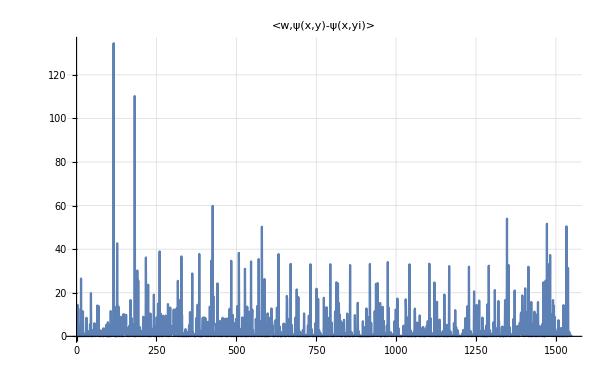

```mathematica
ListLinePlot[d,GridLines->Automatic,PlotLabel->"<w,ψ(x,y)-ψ(x,yi)>",PlotRange->All]
```